# The Chess Package

Load the package:

```mathematica
Needs["Chess`"]
```

Chess piece images were downloaded.

## Pieces and moves

Pieces includes all pieces, including the virtual pieces piece0 and piece33:

```mathematica
{piece0,piece33}
```

{<|id→0,image→{},status→enpassant,pos→{{}}|>,<|id→33,image→{},status→enpassant,pos→{{}}|>}

The properties of each piece is embedded in the association piece#, where # is the piece number.

The image of each piece is downloaded or kept in the mx-file pieceImages.mx:

```mathematica
GraphicsGrid[Partition[#[image]&/@Most@Rest@Pieces,16],ImageSize->500]
```

-Graphics-

Standard positions are obtained by executing Startposition:

```mathematica
Startposition
```

whiteoptionlist and blackoptionlist display move options of all pieces by x- and y-coordinates:

```mathematica
whiteoptionlist
```

<|1→{{1,3},{1,4}},2→{{2,3},{2,4}},3→{{3,3},{3,4}},4→{{4,3},{4,4}},5→{{5,3},{5,4}},6→{{6,3},{6,4}},7→{{7,3},{7,4}},8→{{8,3},{8,4}},9→{{1,3},{3,3}},10→{{6,3},{8,3}}|>

```mathematica
blackoptionlist
```

<|17→{{1,6},{1,5}},18→{{2,6},{2,5}},19→{{3,6},{3,5}},20→{{4,6},{4,5}},21→{{5,6},{5,5}},22→{{6,6},{6,5}},23→{{7,6},{7,5}},24→{{8,6},{8,5}},25→{{1,6},{3,6}},26→{{6,6},{8,6}}|>

A move may be selected randomly by RandomMove:

```mathematica
move1=RandomMove
```

{7,{7,4}}

The status of this piece number is

```mathematica
#[status]&/@Select[Pieces,#[id]===move1[[1]]&]
```

{pawn}

and the move is to

```mathematica
Coord[move1[[2]]]
```

g4

The function Move is used to move the piece:

```mathematica
Move[move1]
```

The situation after the move is displayed by Chess[]:

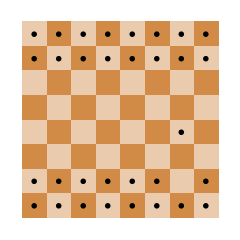

```mathematica
Chess[]
```

Next move could also be randomly found, this time black is to move:

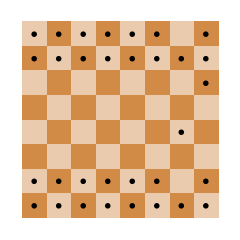

```mathematica
Move[RandomMove];Chess[]
```

And so on ...

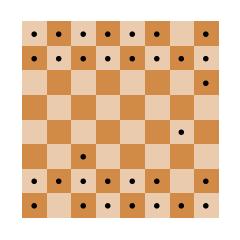

```mathematica
Move[RandomMove];Chess[]
```

## Options

The options regulate how the chessboard should be displayed

```mathematica
Options[Chess]//TableForm
```

ShowBoard→Static
ImageSize→240
PieceSize→Automatic
BoardColour→RGBColor[0.8196, 0.5451, 0.2784]
ShowPieces→All
PawnConvert→MakeQueen
ShowPGN→True
Interact→True

### ShowPieces

ShowPieces may have three values

All - All pieces are displayed (default)

White - Only the white pieces are shown

Black - Only the black pieces are shown

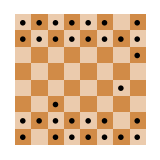
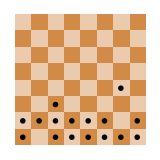
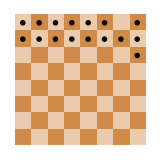

```mathematica
Chess[ShowPieces->#,ImageSize->160]&/@{All,White,Black}
```

### PawnConvert

PawnConvert may have two values

MakeQueen - pawns are converted to queens (default)

Menu - pawns are converted according to interactive choices (not working!!)

### ShowBoard

ShowBoard could have the following values :

None - No chessboard is displayed

Static - The chessboard is displayed with current placement of pieces (default value)

Dynamic - Pieces are allowed to move as they change positions

Random - Pieces can be randomly moved by clicking the displayed buttons

PGN-values - Pieces are moved according to predefined PGN-values

```mathematica
Startposition;
Chess[ShowBoard->Dynamic]
Do[Move[RandomMove];Pause[.3],{10}]
```

```mathematica
Startposition;
Chess[ShowBoard->Interactive]
```

```mathematica
Chess[ShowBoard->Random,ShowPGN->False]
```

RestartBackRandom Move

## Display PGN moves

```mathematica
anand=Import["http://chessproblem.my-free-games.com/PGN/Anand.zip","*.pgn"][[1]];
kasparov=Import["http://chessproblem.my-free-games.com/PGN/Kasparov.zip","*.pgn"][[1]];
alekhine=Import["http://chessproblem.my-free-games.com/PGN/Alekhine.zip","*.pgn"][[1]];
```

```mathematica
ShortPGN[kasparov,200]
```

[Event "World Championship 31th"]
[Site "Moscow RUS"]
[Date "1984.10.31"]
[Round "20"]
[White "Kasparov, Gary"]
[Black "Karpov, Anatoly"]
[Result "1/2-1/2"]
[WhiteElo "2715"]
[BlackElo "2705"]
[ECO "A30f"]
[EventDate "1984.09.10"]

```mathematica
pgn=PGNconvert[kasparov,198]
```

{{4,4},{knight,6,6},{3,4},{5,6},{7,3},{4,5},{bishop,7,2},{bishop,5,7},{knight,6,3},{0,Chess`Private`short},{0,Chess`Private`short},{d,x,3,4},{queen,3,2},{1,6},{queen,x,3,4},{2,5},{queen,3,2},{bishop,2,7},{bishop,4,2},{bishop,5,4},{queen,3,1},{bishop,2,7},{bishop,5,3},{knight,4,5},{knight,3,3},{knight,4,7},{rook,4,1},{rook,3,8},{knight,x,4,5},{bishop,x,4,5},{knight,5,1},{3,6},{knight,4,3},{queen,2,6},{queen,3,3},{2,4},{queen,4,2},{1,5},{rook,d,3,1}}

```mathematica
StringJoin[PGNlisting[kasparov,198][[1,1,3,1]][[{1,4}]]]
```

[Event "World Championship 31th"][Round "8"]

```mathematica
Chess[ShowBoard->pgn,Interact->False]
```

RestartBackNext

```mathematica
PGN//Dynamic
```

```mathematica
PGNlisting[kasparov,198]
```

1 | d4 | Nf6
2 | c4 | e6
3 | g3 | d5
4 | Bg2 | Be7
5 | Nf3 | O-O
6 | O-O | dxc4
7 | Qc2 | a6
8 | Qxc4 | b5
9 | Qc2 | Bb7
10 | Bd2 | Be4
11 | Qc1 | Bb7
12 | Be3 | Nd5
13 | Nc3 | Nd7
14 | Rd1 | Rc8
15 | Nxd5 | Bxd5
16 | Ne1 | c6
17 | Nd3 | Qb6
18 | Qc3 | b4
19 | Qd2 | a5
20 | Rdc1 | 1/2-1/2 | 	 | [Event "World Championship 31th"]
[Site "Moscow RUS"]
[Date "1984.10.03"]
[Round "8"]
[White "Kasparov, Gary"]
[Black "Karpov, Anatoly"]
[Result "1/2-1/2"]
[WhiteElo "2715"]
[BlackElo "2705"]
[ECO "E05t"]
[EventDate "1984.09.10"]